```mathematica
D[1/(-2*a*u^3+b*Sqrt[1-u^4]),u]
```

```mathematica
h[a_,b_,u_]:=Abs[-(-6 a u^2-(2 b u^3)/(√(1-u^4)))/((-2 a u^3+b √(1-u^4))^2)]
```

```mathematica
D[Sqrt[1-u^4],u]
```

-(2 u^3)/(√(1-u^4))

```mathematica
D[-(1-u^2)^(1/4),u]
```

u/(2 (1-u^2)^(3/4))

```mathematica
Det[{{(Sqrt[1-u^4])/2, -2u^3/Sqrt[1-u^4]},{(1/4)*u , 1  } }]//Simplify
```

1/(2 √(1-u^4))

```mathematica
D[-(1-u^2)^(1/4),u]
```

u/(2 (1-u^2)^(3/4))

```mathematica
Det[{{  (1/2)*u  ,   1}, {  -(1-u^2)^(1/4)/4  ,u/(2 (1-u^2)^(3/4)) }}]//Simplify
```

1/(4 (1-u^2)^(3/4))

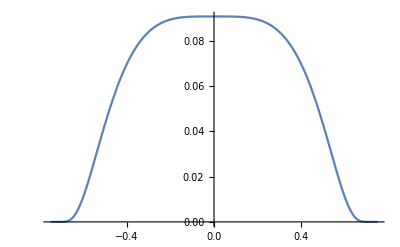

```mathematica
Plot[Exp[1/(Sqrt[1-u^4]^2+0.75^4)]*Exp[1/(u^4-0.75^4)],{u,-0.75,0.75}]
```

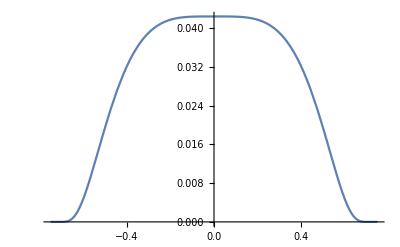

```mathematica
Plot[Exp[1/(u^4-0.75^4)],{u,-0.75,0.75}]
```

```mathematica
D[Exp[1/(x^4-1)],x]//Simplify
```

-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2)

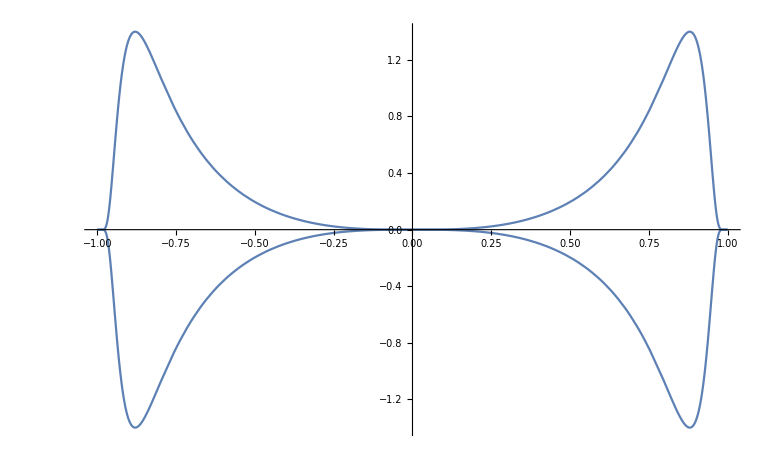

```mathematica
Show[Plot[-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2),{x,-1,1}],Plot[(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2),{x,-1,1}]]
```

```mathematica
-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2)-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2)
```

```mathematica
1/(x^2-1) + 1/(y^4-1)//Simplify
```

1/(-1+x^2)+1/(-1+y^4)

```mathematica
Plot3D[Exp[1/(x^2+y^4-1)],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

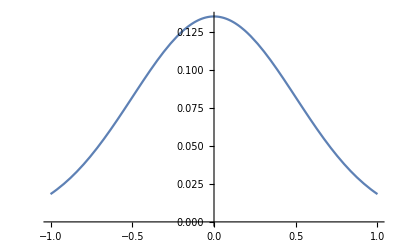

```mathematica
Plot[E^(-(x-1)^2)*E^(-(x+1)^2),{x,-1,1}]
```

```mathematica
Integrate[E^(-(x-1)^2)*E^(-(x+1)^2),{x,0,A}]
```

(√(π/2) Erf[√2 A])/(2 ⅇ^2)

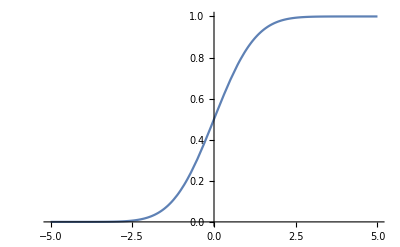

```mathematica
Plot[(1/2)(1+ Erf[u/Sqrt[2]]),{u,-5,5}]
```

```mathematica
D[Sqrt[1-u^4],u]//TeXForm
```

-\frac{2 u^3}{\sqrt{1-u^4}}

```mathematica
D[Sqrt[1-u^4],{u,1}]//FullSimplify
```

-(2 u^3)/(√(1-u^4))

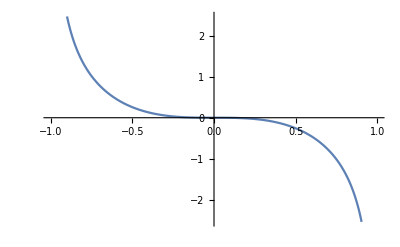

```mathematica
Plot[-(2 u^3)/(√(1-u^4)),{u,-1,1}]
```

```mathematica
D[Sqrt[1-u^4],{u,2}]//FullSimplify
```

(2 u^2 (-3+u^4))/((1-u^4)^(3/2))

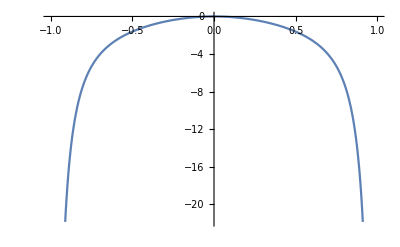

```mathematica
Plot[(2 u^2 (-3+u^4))/((1-u^4)^(3/2)),{u,-1,1}]
```

```mathematica
D[Sqrt[1-u^4],{u,3}]//FullSimplify
```

-(12 (u+u^5))/((1-u^4)^(5/2))

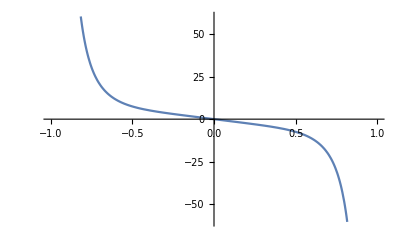

```mathematica
Plot[-(12 (u+u^5))/((1-u^4)^(5/2)),{u,-1,1}]
```

```mathematica
D[Sqrt[1-u^4],{u,4}]//FullSimplify
```

-(12 (1+14 u^4+5 u^8))/((1-u^4)^(7/2))

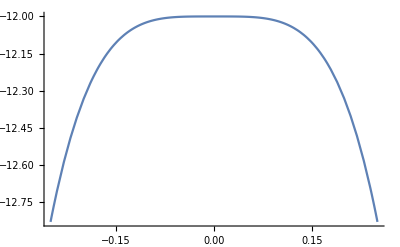

```mathematica
Show[Plot[-(12 (1+14 u^4+5 u^8))/((1-u^4)^(7/2)),{u,-0.25,0.25}],Plot[0,{u,-0.5,0.5}]]
```

```mathematica
D[Sqrt[1-u^4],{u,8}]//FullSimplify
```

-(5040 (1+240 u^4+2190 u^8+3380 u^12+1017 u^16+36 u^20))/((1-u^4)^(15/2))

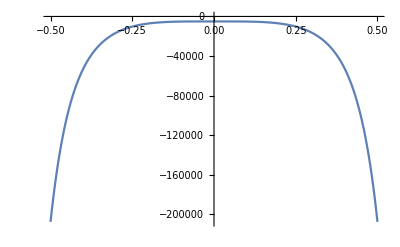

```mathematica
Plot[-(5040 (1+240 u^4+2190 u^8+3380 u^12+1017 u^16+36 u^20))/((1-u^4)^(15/2)),{u,-0.5,0.5}]
```

```mathematica
D[(1-u^2)^(1/4),{u,1}]//FullSimplify
```

-u/(2 (1-u^2)^(3/4))

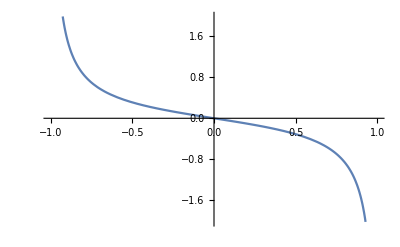

```mathematica
Plot[-u/(2 (1-u^2)^(3/4)),{u,-1,1}]
```

```mathematica
D[(1-u^2)^(1/4),{u,2}]//FullSimplify
```

-(2+u^2)/(4 (1-u^2)^(7/4))

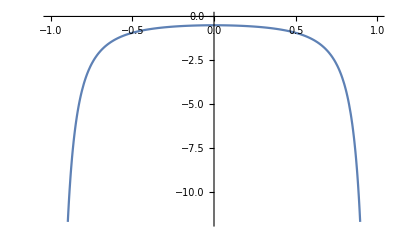

```mathematica
Plot[-(2+u^2)/(4 (1-u^2)^(7/4)),{u,-1,1}]
```